```mathematica
f[z_,c_,b_,0]:=0.0001
f[z_,c_,b_,n_Integer?Positive]:=c  Exp[-I b z+f[b z,c,b,n-1]]-c
c=0.5;
b=1;
m=2.5;
realline= Plot[Re[f[ z ,c,b,100]],{z,0,2π *m/b},PlotRange->All,PlotStyle->{Blue,Thickness[0.002]},AxesLabel->{"z",Row[{"Re(",Subscript[F,η][z],")"}]
},PlotLegends->Placed[{"Numerical solution"},{0.5,-0.01}],PlotLabel->"i) c=" <> ToString[c]<>", β="<>ToString[b]]
```

-Graphics-

```mathematica
Weierstrass =Plot[ Re[(1-c)Sum[(c )^(n) Exp[(-0 n c)-  I z Sum[(b)^r,{r,1,n}]],{n,1,10}]-c],{z,0,2π m/b},PlotStyle->{Thickness[0.002],Red,Dashed},AxesLabel->{"z",Row[{"Re(",Subscript[F,η][z],")"}]},PlotLegends->Placed[{"Series approximation"},{0.5,-0.01}],PlotLabel->"c=" <> ToString[c]<>", β="<>ToString[b]]
```

-Graphics-

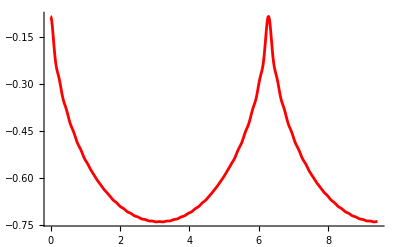

```mathematica
semicircles= Plot[(-c-ProductLog[c Exp[-c]])(π/4+ Sum[((-1)^n  BesselJ[1,π n])/n Cos[n x  ],{n,30}]),{x,0,2π*c m},PlotRange->All,PlotStyle->Red]
```

```mathematica
critical= Plot[Re[-c-ProductLog[-c Exp[-c-I x]]],{x,0,2π*m},PlotRange->All,PlotStyle->{Red,Dashed,Thickness[0.002]},PlotLegends->Placed[{"Exact solution"},{0.5,-0.01}]]
```

-Graphics-

```mathematica
meanppx= Plot[Re[c Exp[-I z b/(1- b c)]]-c,{z,0,m*2π/b},PlotRange->All]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Show[realline,critical,AxisLabel->{"z","Re(Subscript["F",η][z])"},PlotLabel->"ii) c=" <> ToString[c]<>", β="<>ToString[b],PlotLegends->Placed[{"Numerical solution","Series approximation"},{0.5,-0.01}]]
```

-Graphics-

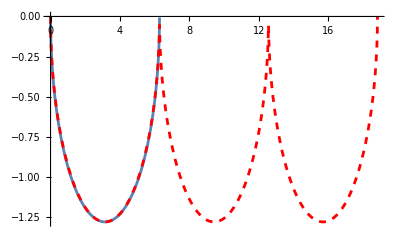

```mathematica
analytic :=Plot[Re[-1-ProductLog[-Exp[-1-I z]]],{z,0,3*2π},PlotStyle->{Red,Dashed}]
circle:= Plot[(-1-ProductLog[Exp[-1]])Sqrt[π^2-(z-π)^2]/π,{z,0,m*2π}]
Show[circle,analytic]
```

```mathematica
Sum[Exp[-I w (2n+1)]/((2n+1)(1+I w (2n+1))),{n,0,Infinity}]
```

(ⅇ^(-ⅈ w) (-ⅈ ⅇ^(ⅈ w) ArcTanh[ⅇ^(-ⅈ w)]+ⅇ^(ⅈ w) w ArcTanh[ⅇ^(-ⅈ w)]-w Hypergeometric2F1[1,1/2-ⅈ/(2 w),3/2-ⅈ/(2 w),ⅇ^(-2 ⅈ w)]))/(-ⅈ+w)

```mathematica
Integrate[Exp[I z/p^k] (-I z/p),{z,-Infinity,Infinity}]
```

Integrate::idiv: Integral of -(ⅈ ⅇ^(ⅈ p^-k z) z)/p does not converge on {-∞,∞}.

∫_(-∞)^∞ -(ⅈ ⅇ^(ⅈ p^-k z) z)/pⅆz

General::munfl: Exp[-1021.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3394.57] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11304.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

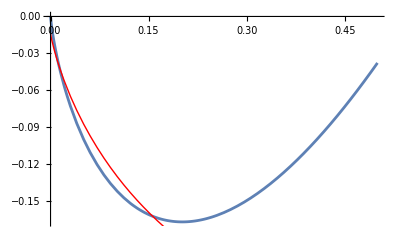

```mathematica
matcher =Plot[ Re[Sum[(c )^(n) Exp[(-n c)-   z Sum[b^r,{r,1,n}]],{n,1,20}]-c],{z,0,0.5},PlotStyle->{Thin,Red}];
power= Plot[-z Log[z]/Log[c]+0.5z,{z,0,0.5}];
Show[power,matcher]
```

```mathematica
SeriesCoefficient[Sum[g[k] Sum[a[n-1]Exp[-I k z Sum[1/p^i,{i,2,n}]],{n,2,Infinity}],{k,1,Infinity}],Exp[-I l z Sum[1/p^i,{i,2,n}]]]
```

SeriesCoefficient[∑_(k=1)^∞ g[k] ∑_(n=2)^∞ ⅇ^(-(ⅈ k p^(-1-n) (-p+p^n) z)/(-1+p)) a[-1+n],ⅇ^(-(ⅈ l p^(-1-n) (-p+p^n) z)/(-1+p))]

```mathematica
FullSimplify[x Exp[-x]/(1-y)  (1/(1-x Exp[-x])-y^2/(1-x Exp[-x]y))-x Exp[-x]/(1-x Exp[-x])]
```

(ⅇ^x x y)/((ⅇ^x-x) (ⅇ^x-x y))

```mathematica
Weierstrass =Plot[ Re[Sum[(c )^(n) Exp[(-n c)-  I z Sum[b^r,{r,1,n}]],{n,1,10}]-c],{z,0,2π m/b},PlotStyle->{Thin,Red}]
```